```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

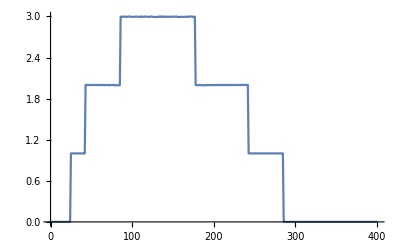

```mathematica
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,4,0.01}]]
```

```mathematica
imp1[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2[ω_,ϵ2_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ2=RandomInteger[{1,14}]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ2]]];imp[ω_,ϵ2_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ2=RandomInteger[{1,14}]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-0]]]
```

```mathematica
RandomSample[Join[Table[imp1[ω,ϵ1],14*1],Table[imp2[ω,ϵ2],14*2],Table[imp[ω,ϵ2],100-14*3]]]
```

{imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1]}

```mathematica
Dimensions[%16]
```

{100}

```mathematica
m1020[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1]},
tra1:=Module[{},
b=Module[{},
lista={RandomSample[{imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1]}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,Mean[Table[m1020[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m1020[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000271077},{0.01,0.0000375361},{0.02,0.0000221154},{0.03,0.0000447866},{0.04,0.0000576919},{0.05,0.0000884149},{0.06,0.000121431},{0.07,0.00017062},{0.08,0.000233208},{0.09,0.000284282},{0.1,0.000381095},{0.11,0.000471126},{0.12,0.000638209},{0.13,0.000780018},{0.14,0.0010091},{0.15,0.00124262},{0.16,0.00158257},{0.17,0.00216127},{0.18,0.00255347},{0.19,0.00367978},{0.2,0.00525891},{0.21,0.00736623},{0.22,0.0115541},{0.23,0.0249916},{0.24,0.086962},{0.25,0.13173},{0.26,0.162331},{0.27,0.21288},{0.28,0.262473},{0.29,0.30767},{0.3,0.329216},{0.31,0.380515},{0.32,0.400553},{0.33,0.409154},{0.34,0.443424},{0.35,0.446502},{0.36,0.469917},{0.37,0.458335},{0.38,0.467144},{0.39,0.467936},{0.4,0.457093},{0.41,0.451419},{0.42,0.938378},{0.43,1.39111},{0.44,1.00444},{0.45,0.780947},{0.46,0.652484},{0.47,0.572055},{0.48,0.544757},{0.49,0.543427},{0.5,0.559429},{0.51,0.546877},{0.52,0.569462},{0.53,0.594507},{0.54,0.591823},{0.55,0.64337},{0.56,0.634579},{0.57,0.68323},{0.58,0.692754},{0.59,0.688446},{0.6,0.729349},{0.61,0.756025},{0.62,0.765156},{0.63,0.780033},{0.64,0.819499},{0.65,0.814452},{0.66,0.841416},{0.67,0.847993},{0.68,0.846663},{0.69,0.879304},{0.7,0.869459},{0.71,0.886534},{0.72,0.898788},{0.73,0.917151},{0.74,0.96642},{0.75,0.942547},{0.76,0.963983},{0.77,0.967555},{0.78,0.994449},{0.79,1.00054},{0.8,1.03122},{0.81,1.01748},{0.82,1.01351},{0.83,1.01026},{0.84,0.94787},{0.85,0.9984},{0.86,1.19164},{0.87,1.1042},{0.88,0.824348},{0.89,0.685524},{0.9,0.65611},{0.91,0.626068},{0.92,0.652176},{0.93,0.701974},{0.94,0.740912},{0.95,0.753148},{0.96,0.818154},{0.97,0.881709},{0.98,0.930574},{0.99,0.91161},{1.,0.956781},{1.01,1.1055},{1.02,1.03521},{1.03,0.747869},{1.04,0.37088},{1.05,0.562449},{1.06,0.558436},{1.07,0.457162},{1.08,0.371119},{1.09,0.334006},{1.1,0.314359},{1.11,0.352721},{1.12,0.336866},{1.13,0.335747},{1.14,0.329622},{1.15,0.324935},{1.16,0.302768},{1.17,0.300044},{1.18,0.306658},{1.19,0.314697},{1.2,0.319355},{1.21,0.341139},{1.22,0.344474},{1.23,0.372325},{1.24,0.37074},{1.25,0.392427},{1.26,0.41216},{1.27,0.405326},{1.28,0.409698},{1.29,0.424077},{1.3,0.427904},{1.31,0.458207},{1.32,0.444654},{1.33,0.470642},{1.34,0.449092},{1.35,0.472547},{1.36,0.479731},{1.37,0.494685},{1.38,0.493894},{1.39,0.465853},{1.4,0.475833},{1.41,0.493644},{1.42,0.483369},{1.43,0.483125},{1.44,0.490323},{1.45,0.475152},{1.46,0.468089},{1.47,0.480835},{1.48,0.465883},{1.49,0.483731},{1.5,0.48951}}

{{0.,0.0000121957},{0.01,0.0000100999},{0.02,0.0000118735},{0.03,0.0000202041},{0.04,0.0000339411},{0.05,0.0000536178},{0.06,0.0000692206},{0.07,0.000110139},{0.08,0.000131173},{0.09,0.000192567},{0.1,0.000238214},{0.11,0.000281942},{0.12,0.00039983},{0.13,0.000512126},{0.14,0.000619772},{0.15,0.000754561},{0.16,0.000932894},{0.17,0.00121158},{0.18,0.00168297},{0.19,0.00225125},{0.2,0.00313562},{0.21,0.00488907},{0.22,0.0072236},{0.23,0.019449},{0.24,0.0736067},{0.25,0.169754},{0.26,0.257487},{0.27,0.337225},{0.28,0.412085},{0.29,0.460082},{0.3,0.496579},{0.31,0.52787},{0.32,0.55976},{0.33,0.568416},{0.34,0.571476},{0.35,0.595958},{0.36,0.609722},{0.37,0.607948},{0.38,0.609252},{0.39,0.612174},{0.4,0.592838},{0.41,0.548999},{0.42,0.842136},{0.43,1.18775},{0.44,0.806126},{0.45,0.663228},{0.46,0.625003},{0.47,0.627009},{0.48,0.676022},{0.49,0.704975},{0.5,0.759795},{0.51,0.792752},{0.52,0.808742},{0.53,0.829147},{0.54,0.865142},{0.55,0.922787},{0.56,0.946888},{0.57,0.97681},{0.58,1.00392},{0.59,0.992174},{0.6,1.04405},{0.61,1.06459},{0.62,1.07452},{0.63,1.07585},{0.64,1.09948},{0.65,1.11967},{0.66,1.14},{0.67,1.14766},{0.68,1.13878},{0.69,1.17052},{0.7,1.18523},{0.71,1.19275},{0.72,1.19684},{0.73,1.20131},{0.74,1.24172},{0.75,1.2365},{0.76,1.23857},{0.77,1.23955},{0.78,1.27155},{0.79,1.2729},{0.8,1.3027},{0.81,1.30807},{0.82,1.30182},{0.83,1.30271},{0.84,1.24884},{0.85,0.950417},{0.86,1.1396},{0.87,0.887198},{0.88,0.754727},{0.89,0.767229},{0.9,0.827474},{0.91,0.898206},{0.92,0.992053},{0.93,1.06697},{0.94,1.15149},{0.95,1.19864},{0.96,1.26296},{0.97,1.3324},{0.98,1.41019},{0.99,1.42823},{1.,1.42753},{1.01,1.55817},{1.02,1.4159},{1.03,0.775481},{1.04,0.328504},{1.05,0.5536},{1.06,0.741317},{1.07,0.693894},{1.08,0.555324},{1.09,0.428706},{1.1,0.365935},{1.11,0.333565},{1.12,0.340731},{1.13,0.335746},{1.14,0.343565},{1.15,0.368032},{1.16,0.408741},{1.17,0.438343},{1.18,0.484918},{1.19,0.507424},{1.2,0.564356},{1.21,0.604398},{1.22,0.648888},{1.23,0.687494},{1.24,0.671664},{1.25,0.734554},{1.26,0.75667},{1.27,0.762242},{1.28,0.767816},{1.29,0.771168},{1.3,0.802768},{1.31,0.802098},{1.32,0.821452},{1.33,0.857503},{1.34,0.818475},{1.35,0.853744},{1.36,0.861448},{1.37,0.891923},{1.38,0.88263},{1.39,0.839541},{1.4,0.855643},{1.41,0.879473},{1.42,0.850935},{1.43,0.836598},{1.44,0.853802},{1.45,0.823467},{1.46,0.8024},{1.47,0.83333},{1.48,0.844107},{1.49,0.852746},{1.5,0.859396}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_20t30.dat",%194]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_10t30.dat",%195]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_10_nb_20t30.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_10t30.dat

```mathematica
m2520[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1]},
tra1:=Module[{},
b=Module[{},
lista={RandomSample[{imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2]}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,Mean[Table[m2520[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m2520[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000375827},{0.01,0.0000413797},{0.02,0.0000265659},{0.03,0.0000441764},{0.04,0.0000528536},{0.05,0.0000874044},{0.06,0.000125328},{0.07,0.000177258},{0.08,0.000235923},{0.09,0.000304015},{0.1,0.000384033},{0.11,0.000507874},{0.12,0.000676893},{0.13,0.000738355},{0.14,0.0011165},{0.15,0.00124425},{0.16,0.00163771},{0.17,0.00222203},{0.18,0.00286199},{0.19,0.00405192},{0.2,0.00541519},{0.21,0.00743931},{0.22,0.0119219},{0.23,0.0238335},{0.24,0.0705421},{0.25,0.109004},{0.26,0.140103},{0.27,0.185811},{0.28,0.240731},{0.29,0.288269},{0.3,0.320167},{0.31,0.356139},{0.32,0.384131},{0.33,0.391291},{0.34,0.425966},{0.35,0.420884},{0.36,0.425269},{0.37,0.43808},{0.38,0.436325},{0.39,0.441892},{0.4,0.432066},{0.41,0.450271},{0.42,0.714395},{0.43,1.09111},{0.44,1.09824},{0.45,0.823903},{0.46,0.687736},{0.47,0.580652},{0.48,0.557052},{0.49,0.544454},{0.5,0.520333},{0.51,0.514628},{0.52,0.547539},{0.53,0.560442},{0.54,0.576918},{0.55,0.585624},{0.56,0.614329},{0.57,0.639911},{0.58,0.654487},{0.59,0.652659},{0.6,0.701005},{0.61,0.697549},{0.62,0.723447},{0.63,0.728219},{0.64,0.753675},{0.65,0.760949},{0.66,0.793313},{0.67,0.78878},{0.68,0.79408},{0.69,0.828722},{0.7,0.818167},{0.71,0.851459},{0.72,0.845061},{0.73,0.86715},{0.74,0.901954},{0.75,0.895788},{0.76,0.897882},{0.77,0.901798},{0.78,0.927513},{0.79,0.937446},{0.8,0.967897},{0.81,0.94894},{0.82,0.944889},{0.83,0.944493},{0.84,0.879421},{0.85,0.863271},{0.86,1.03988},{0.87,1.14032},{0.88,0.873642},{0.89,0.696551},{0.9,0.661317},{0.91,0.621648},{0.92,0.602419},{0.93,0.651672},{0.94,0.673557},{0.95,0.702673},{0.96,0.770233},{0.97,0.777604},{0.98,0.853331},{0.99,0.888983},{1.,0.893776},{1.01,1.04646},{1.02,0.934647},{1.03,0.562876},{1.04,0.331559},{1.05,0.419876},{1.06,0.454055},{1.07,0.401405},{1.08,0.349512},{1.09,0.331548},{1.1,0.324361},{1.11,0.355169},{1.12,0.343845},{1.13,0.348569},{1.14,0.335156},{1.15,0.329907},{1.16,0.301815},{1.17,0.312122},{1.18,0.313423},{1.19,0.31534},{1.2,0.319353},{1.21,0.340984},{1.22,0.332523},{1.23,0.349731},{1.24,0.360263},{1.25,0.373372},{1.26,0.395016},{1.27,0.396434},{1.28,0.407974},{1.29,0.401939},{1.3,0.423738},{1.31,0.42168},{1.32,0.438087},{1.33,0.443546},{1.34,0.424672},{1.35,0.449275},{1.36,0.446205},{1.37,0.460831},{1.38,0.466539},{1.39,0.439165},{1.4,0.453512},{1.41,0.441892},{1.42,0.441398},{1.43,0.451514},{1.44,0.45809},{1.45,0.440461},{1.46,0.442112},{1.47,0.456694},{1.48,0.446653},{1.49,0.461598},{1.5,0.455458}}

{{0.,0.0000601587},{0.01,0.0000353035},{0.02,0.0000426818},{0.03,0.0000532504},{0.04,0.0000635517},{0.05,0.000102585},{0.06,0.000148761},{0.07,0.000196306},{0.08,0.000259296},{0.09,0.00037554},{0.1,0.000454997},{0.11,0.000605376},{0.12,0.000758592},{0.13,0.000949789},{0.14,0.0011992},{0.15,0.00150568},{0.16,0.00185417},{0.17,0.00260729},{0.18,0.00310958},{0.19,0.00424047},{0.2,0.00568421},{0.21,0.00863089},{0.22,0.0133447},{0.23,0.026111},{0.24,0.0669089},{0.25,0.0993532},{0.26,0.134599},{0.27,0.166745},{0.28,0.195168},{0.29,0.243897},{0.3,0.281836},{0.31,0.3024},{0.32,0.319731},{0.33,0.336533},{0.34,0.361192},{0.35,0.376738},{0.36,0.381354},{0.37,0.388513},{0.38,0.393953},{0.39,0.403922},{0.4,0.402093},{0.41,0.44013},{0.42,0.797134},{0.43,1.09724},{0.44,1.11503},{0.45,0.901002},{0.46,0.715903},{0.47,0.620762},{0.48,0.54826},{0.49,0.541269},{0.5,0.513679},{0.51,0.489705},{0.52,0.508092},{0.53,0.511863},{0.54,0.502222},{0.55,0.531309},{0.56,0.550958},{0.57,0.554911},{0.58,0.569547},{0.59,0.571974},{0.6,0.587145},{0.61,0.632122},{0.62,0.639324},{0.63,0.634375},{0.64,0.657013},{0.65,0.662833},{0.66,0.691168},{0.67,0.695145},{0.68,0.707937},{0.69,0.718444},{0.7,0.73055},{0.71,0.74526},{0.72,0.752441},{0.73,0.749631},{0.74,0.801385},{0.75,0.787659},{0.76,0.787354},{0.77,0.798982},{0.78,0.838601},{0.79,0.83133},{0.8,0.852622},{0.81,0.841329},{0.82,0.835298},{0.83,0.837942},{0.84,0.782781},{0.85,0.92947},{0.86,1.01765},{0.87,1.16779},{0.88,0.883358},{0.89,0.74045},{0.9,0.681498},{0.91,0.592025},{0.92,0.57672},{0.93,0.575951},{0.94,0.597817},{0.95,0.613358},{0.96,0.664358},{0.97,0.687749},{0.98,0.726362},{0.99,0.737389},{1.,0.744577},{1.01,0.890857},{1.02,0.848342},{1.03,0.558496},{1.04,0.345869},{1.05,0.41593},{1.06,0.427812},{1.07,0.378613},{1.08,0.344308},{1.09,0.335168},{1.1,0.322954},{1.11,0.352384},{1.12,0.370577},{1.13,0.362444},{1.14,0.342574},{1.15,0.346021},{1.16,0.291969},{1.17,0.317746},{1.18,0.297971},{1.19,0.30372},{1.2,0.297949},{1.21,0.314766},{1.22,0.303188},{1.23,0.312628},{1.24,0.338188},{1.25,0.319128},{1.26,0.332526},{1.27,0.345117},{1.28,0.3486},{1.29,0.352919},{1.3,0.335844},{1.31,0.348379},{1.32,0.371485},{1.33,0.376664},{1.34,0.358147},{1.35,0.369606},{1.36,0.379385},{1.37,0.371604},{1.38,0.390729},{1.39,0.379564},{1.4,0.374416},{1.41,0.382154},{1.42,0.388565},{1.43,0.371672},{1.44,0.376612},{1.45,0.387645},{1.46,0.383373},{1.47,0.390281},{1.48,0.382351},{1.49,0.381339},{1.5,0.376547}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_20t45.dat",%27]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_25t45.dat",%28]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_20t45.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_25t45.dat

```mathematica
m3020[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1]},
tra1:=Module[{},
b=Module[{},
lista={RandomSample[{imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2]}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,Mean[Table[m3020[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m3020[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000379507},{0.01,0.0000220814},{0.02,0.0000288265},{0.03,0.0000418223},{0.04,0.0000604079},{0.05,0.0000929957},{0.06,0.00012493},{0.07,0.000173494},{0.08,0.00021874},{0.09,0.000302526},{0.1,0.000420856},{0.11,0.000513662},{0.12,0.000637509},{0.13,0.000811834},{0.14,0.00102859},{0.15,0.00134016},{0.16,0.0018063},{0.17,0.00221581},{0.18,0.00281666},{0.19,0.00353225},{0.2,0.00548952},{0.21,0.00750095},{0.22,0.0116503},{0.23,0.0248048},{0.24,0.0643178},{0.25,0.0890966},{0.26,0.138146},{0.27,0.17766},{0.28,0.243195},{0.29,0.266086},{0.3,0.316524},{0.31,0.339082},{0.32,0.374545},{0.33,0.392864},{0.34,0.396546},{0.35,0.416907},{0.36,0.424089},{0.37,0.434311},{0.38,0.422073},{0.39,0.427951},{0.4,0.443864},{0.41,0.445153},{0.42,0.701671},{0.43,0.998768},{0.44,1.04642},{0.45,0.851287},{0.46,0.695483},{0.47,0.606635},{0.48,0.549662},{0.49,0.542354},{0.5,0.517731},{0.51,0.522818},{0.52,0.538563},{0.53,0.542262},{0.54,0.545658},{0.55,0.588094},{0.56,0.596854},{0.57,0.62294},{0.58,0.647444},{0.59,0.635459},{0.6,0.669559},{0.61,0.706224},{0.62,0.715378},{0.63,0.715238},{0.64,0.739549},{0.65,0.75275},{0.66,0.766536},{0.67,0.777891},{0.68,0.776801},{0.69,0.805887},{0.7,0.811039},{0.71,0.826785},{0.72,0.83477},{0.73,0.851339},{0.74,0.881105},{0.75,0.874291},{0.76,0.884101},{0.77,0.858734},{0.78,0.91758},{0.79,0.925405},{0.8,0.949354},{0.81,0.918975},{0.82,0.914391},{0.83,0.919521},{0.84,0.861084},{0.85,0.844965},{0.86,0.984232},{0.87,1.12238},{0.88,0.864518},{0.89,0.708727},{0.9,0.6501},{0.91,0.593348},{0.92,0.608087},{0.93,0.624934},{0.94,0.678959},{0.95,0.678243},{0.96,0.726116},{0.97,0.773195},{0.98,0.858426},{0.99,0.855534},{1.,0.869911},{1.01,1.03157},{1.02,0.910393},{1.03,0.527477},{1.04,0.338289},{1.05,0.389502},{1.06,0.437538},{1.07,0.401427},{1.08,0.357741},{1.09,0.326345},{1.1,0.329118},{1.11,0.355657},{1.12,0.355588},{1.13,0.348766},{1.14,0.331694},{1.15,0.337529},{1.16,0.304614},{1.17,0.315278},{1.18,0.306565},{1.19,0.318912},{1.2,0.32234},{1.21,0.330571},{1.22,0.339575},{1.23,0.341971},{1.24,0.36372},{1.25,0.369398},{1.26,0.391523},{1.27,0.374847},{1.28,0.401412},{1.29,0.393605},{1.3,0.414226},{1.31,0.421352},{1.32,0.399075},{1.33,0.433636},{1.34,0.40976},{1.35,0.441319},{1.36,0.438955},{1.37,0.453057},{1.38,0.449814},{1.39,0.431754},{1.4,0.428986},{1.41,0.445453},{1.42,0.433055},{1.43,0.443947},{1.44,0.442775},{1.45,0.430756},{1.46,0.428311},{1.47,0.431751},{1.48,0.430433},{1.49,0.445181},{1.5,0.435907}}

{{0.,0.0000762199},{0.01,0.0000559696},{0.02,0.0000526467},{0.03,0.0000654988},{0.04,0.000085075},{0.05,0.000125846},{0.06,0.000168553},{0.07,0.000214913},{0.08,0.000305609},{0.09,0.000426912},{0.1,0.000518981},{0.11,0.000654217},{0.12,0.000840264},{0.13,0.00110397},{0.14,0.00135679},{0.15,0.00169656},{0.16,0.00225922},{0.17,0.00264883},{0.18,0.0036665},{0.19,0.00479928},{0.2,0.00658783},{0.21,0.00933506},{0.22,0.0150395},{0.23,0.0298162},{0.24,0.0723905},{0.25,0.0937193},{0.26,0.125128},{0.27,0.143897},{0.28,0.178428},{0.29,0.211453},{0.3,0.242039},{0.31,0.255795},{0.32,0.283227},{0.33,0.293472},{0.34,0.310099},{0.35,0.324594},{0.36,0.346957},{0.37,0.348877},{0.38,0.353074},{0.39,0.35009},{0.4,0.366323},{0.41,0.440896},{0.42,0.817079},{0.43,0.985952},{0.44,1.09745},{0.45,0.952076},{0.46,0.777396},{0.47,0.639903},{0.48,0.580394},{0.49,0.537696},{0.5,0.490569},{0.51,0.472738},{0.52,0.473375},{0.53,0.463127},{0.54,0.476649},{0.55,0.462968},{0.56,0.487665},{0.57,0.494626},{0.58,0.497937},{0.59,0.500719},{0.6,0.539627},{0.61,0.542073},{0.62,0.549936},{0.63,0.55547},{0.64,0.570914},{0.65,0.575576},{0.66,0.598104},{0.67,0.613576},{0.68,0.623783},{0.69,0.638537},{0.7,0.625652},{0.71,0.644861},{0.72,0.668667},{0.73,0.671735},{0.74,0.711707},{0.75,0.697854},{0.76,0.708856},{0.77,0.701504},{0.78,0.740323},{0.79,0.737012},{0.8,0.757443},{0.81,0.74732},{0.82,0.721554},{0.83,0.732419},{0.84,0.683454},{0.85,0.909377},{0.86,0.884059},{0.87,1.15043},{0.88,1.0135},{0.89,0.766157},{0.9,0.70874},{0.91,0.611735},{0.92,0.574027},{0.93,0.551686},{0.94,0.558874},{0.95,0.562305},{0.96,0.584312},{0.97,0.598207},{0.98,0.619621},{0.99,0.625168},{1.,0.639822},{1.01,0.772765},{1.02,0.738579},{1.03,0.517313},{1.04,0.345091},{1.05,0.393461},{1.06,0.388377},{1.07,0.358826},{1.08,0.331698},{1.09,0.344278},{1.1,0.33576},{1.11,0.373204},{1.12,0.373305},{1.13,0.365288},{1.14,0.359203},{1.15,0.362204},{1.16,0.306871},{1.17,0.31553},{1.18,0.288239},{1.19,0.312095},{1.2,0.291485},{1.21,0.295799},{1.22,0.298769},{1.23,0.295956},{1.24,0.323311},{1.25,0.313219},{1.26,0.297522},{1.27,0.315004},{1.28,0.316311},{1.29,0.316798},{1.3,0.309106},{1.31,0.32497},{1.32,0.330351},{1.33,0.333562},{1.34,0.334555},{1.35,0.326573},{1.36,0.322533},{1.37,0.334989},{1.38,0.336221},{1.39,0.347032},{1.4,0.334853},{1.41,0.345098},{1.42,0.354716},{1.43,0.352692},{1.44,0.331028},{1.45,0.353695},{1.46,0.339524},{1.47,0.339274},{1.48,0.339325},{1.49,0.331371},{1.5,0.335341}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_20t50.dat",%30]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_30t50.dat",%31]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_20t50.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_30t50.dat

```mathematica
m3025[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1]},
tra1:=Module[{},
b=Module[{},
lista={RandomSample[{imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp2[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp2[ω,ϵ2],imp[ω,ϵ2],imp2[ω,ϵ2],imp1[ω,ϵ1],imp1[ω,ϵ1],imp1[ω,ϵ1],imp2[ω,ϵ2],imp1[ω,ϵ1]}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,Mean[Table[m3025[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
Table[{ω,Mean[Table[m3025[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000708317},{0.01,0.0000552647},{0.02,0.0000480919},{0.03,0.0000480586},{0.04,0.0000710823},{0.05,0.000102184},{0.06,0.000135216},{0.07,0.000185302},{0.08,0.00027264},{0.09,0.000362183},{0.1,0.000484974},{0.11,0.000613132},{0.12,0.000780844},{0.13,0.000922012},{0.14,0.00121361},{0.15,0.00154354},{0.16,0.00206973},{0.17,0.00251231},{0.18,0.00338033},{0.19,0.004438},{0.2,0.00572114},{0.21,0.00809439},{0.22,0.01322},{0.23,0.0250281},{0.24,0.0687542},{0.25,0.0876064},{0.26,0.130574},{0.27,0.161733},{0.28,0.189288},{0.29,0.233412},{0.3,0.264091},{0.31,0.293688},{0.32,0.310992},{0.33,0.338113},{0.34,0.351733},{0.35,0.353832},{0.36,0.372662},{0.37,0.381173},{0.38,0.374214},{0.39,0.378454},{0.4,0.383051},{0.41,0.423101},{0.42,0.703795},{0.43,0.883362},{0.44,1.06555},{0.45,0.924403},{0.46,0.703024},{0.47,0.630761},{0.48,0.548242},{0.49,0.521415},{0.5,0.507816},{0.51,0.483003},{0.52,0.49166},{0.53,0.493149},{0.54,0.515363},{0.55,0.516866},{0.56,0.539259},{0.57,0.539777},{0.58,0.560521},{0.59,0.549429},{0.6,0.580539},{0.61,0.605111},{0.62,0.604056},{0.63,0.621596},{0.64,0.64978},{0.65,0.642127},{0.66,0.666708},{0.67,0.666237},{0.68,0.690711},{0.69,0.708295},{0.7,0.715188},{0.71,0.727553},{0.72,0.71904},{0.73,0.749308},{0.74,0.757466},{0.75,0.77268},{0.76,0.784082},{0.77,0.769328},{0.78,0.798808},{0.79,0.817201},{0.8,0.830927},{0.81,0.805435},{0.82,0.808317},{0.83,0.809757},{0.84,0.749077},{0.85,0.831622},{0.86,0.868139},{0.87,1.16317},{0.88,0.984044},{0.89,0.741215},{0.9,0.709258},{0.91,0.590745},{0.92,0.578539},{0.93,0.572582},{0.94,0.581347},{0.95,0.597215},{0.96,0.622891},{0.97,0.646834},{0.98,0.703209},{0.99,0.711544},{1.,0.732047},{1.01,0.860599},{1.02,0.794692},{1.03,0.493436},{1.04,0.343216},{1.05,0.383079},{1.06,0.397236},{1.07,0.369577},{1.08,0.342806},{1.09,0.342632},{1.1,0.332341},{1.11,0.356648},{1.12,0.370108},{1.13,0.366188},{1.14,0.352151},{1.15,0.347881},{1.16,0.303096},{1.17,0.306595},{1.18,0.297622},{1.19,0.306767},{1.2,0.295799},{1.21,0.310702},{1.22,0.301548},{1.23,0.307973},{1.24,0.336807},{1.25,0.330017},{1.26,0.321049},{1.27,0.338107},{1.28,0.341273},{1.29,0.348665},{1.3,0.348952},{1.31,0.345255},{1.32,0.360161},{1.33,0.356853},{1.34,0.363271},{1.35,0.361965},{1.36,0.368657},{1.37,0.362315},{1.38,0.372891},{1.39,0.378896},{1.4,0.365564},{1.41,0.366108},{1.42,0.371479},{1.43,0.366682},{1.44,0.371085},{1.45,0.36711},{1.46,0.363673},{1.47,0.367685},{1.48,0.364074},{1.49,0.373612},{1.5,0.36921}}

{{0.,0.0000743995},{0.01,0.0000505225},{0.02,0.0000523958},{0.03,0.000068129},{0.04,0.00008731},{0.05,0.000107093},{0.06,0.000160526},{0.07,0.000213295},{0.08,0.000289812},{0.09,0.000391605},{0.1,0.000510515},{0.11,0.000675218},{0.12,0.000842865},{0.13,0.00104868},{0.14,0.00131396},{0.15,0.0018621},{0.16,0.00209502},{0.17,0.00283439},{0.18,0.00360537},{0.19,0.00489682},{0.2,0.0066203},{0.21,0.00953721},{0.22,0.015107},{0.23,0.0266858},{0.24,0.0724133},{0.25,0.0883211},{0.26,0.123376},{0.27,0.143479},{0.28,0.172414},{0.29,0.204771},{0.3,0.236229},{0.31,0.262097},{0.32,0.276104},{0.33,0.294223},{0.34,0.311523},{0.35,0.32205},{0.36,0.340961},{0.37,0.336282},{0.38,0.33996},{0.39,0.358302},{0.4,0.347839},{0.41,0.436289},{0.42,0.749312},{0.43,0.861912},{0.44,1.0614},{0.45,0.966714},{0.46,0.775062},{0.47,0.653115},{0.48,0.57218},{0.49,0.530347},{0.5,0.508991},{0.51,0.461041},{0.52,0.468626},{0.53,0.4719},{0.54,0.46182},{0.55,0.466943},{0.56,0.485193},{0.57,0.487069},{0.58,0.489604},{0.59,0.497935},{0.6,0.520767},{0.61,0.546061},{0.62,0.527534},{0.63,0.547859},{0.64,0.580379},{0.65,0.577078},{0.66,0.612047},{0.67,0.597916},{0.68,0.60598},{0.69,0.629736},{0.7,0.621953},{0.71,0.643716},{0.72,0.646504},{0.73,0.662735},{0.74,0.690021},{0.75,0.678438},{0.76,0.688001},{0.77,0.684234},{0.78,0.743168},{0.79,0.717136},{0.8,0.750208},{0.81,0.735689},{0.82,0.716215},{0.83,0.704413},{0.84,0.670106},{0.85,0.864759},{0.86,0.870139},{0.87,1.11679},{0.88,0.993493},{0.89,0.811543},{0.9,0.716428},{0.91,0.604802},{0.92,0.581393},{0.93,0.54472},{0.94,0.553269},{0.95,0.56693},{0.96,0.567173},{0.97,0.59727},{0.98,0.612822},{0.99,0.633132},{1.,0.646816},{1.01,0.746074},{1.02,0.713552},{1.03,0.483788},{1.04,0.345534},{1.05,0.386311},{1.06,0.390201},{1.07,0.359575},{1.08,0.347353},{1.09,0.327652},{1.1,0.347574},{1.11,0.375122},{1.12,0.381009},{1.13,0.365198},{1.14,0.364621},{1.15,0.360468},{1.16,0.324662},{1.17,0.314732},{1.18,0.301892},{1.19,0.31436},{1.2,0.285435},{1.21,0.303877},{1.22,0.283917},{1.23,0.287477},{1.24,0.318892},{1.25,0.309444},{1.26,0.305207},{1.27,0.314462},{1.28,0.319167},{1.29,0.321382},{1.3,0.319551},{1.31,0.32954},{1.32,0.321549},{1.33,0.329118},{1.34,0.335813},{1.35,0.325298},{1.36,0.331072},{1.37,0.321621},{1.38,0.326534},{1.39,0.34748},{1.4,0.341243},{1.41,0.334365},{1.42,0.33514},{1.43,0.347939},{1.44,0.339385},{1.45,0.337089},{1.46,0.347827},{1.47,0.337692},{1.48,0.331443},{1.49,0.33627},{1.5,0.334539}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_25t55.dat",%33]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_30t55.dat",%34]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_30_nb_25t55.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_25_nb_30t55.dat